RAYLEIGH QAM :

```mathematica
Q[z_]:=1/2 Erfc[z/(√2)];pdf[γ_,γm_]:= 1/10^(γm/10)Exp[-γ/10^(γm/10)];
probErrorQAM[γ_,L_]:=4/Log[2,L](1-2^((-Log[2,L])/2))Q[√((3 γ Log[2,L])/(L-1))];
BERRAYQAM[γm_,L_] := Re[Integrate[probErrorQAM[γ,L]×pdf[γ, γm], {γ,0,∞}]];
```

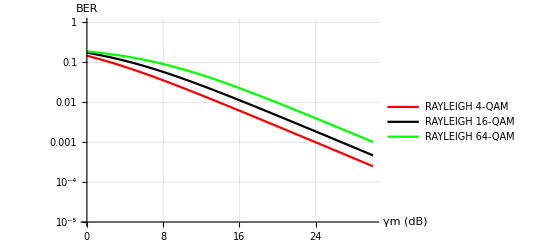

```mathematica
LogPlot[{BERRAYQAM[γm,4], BERRAYQAM[γm,16], BERRAYQAM[γm,64]},{γm,0,30},AxesLabel->{"γm (dB)","BER"},PlotRange->{10^-5,1}, PlotStyle->{Red, Black, Green},PlotLegends->{"RAYLEIGH 4-QAM","RAYLEIGH 16-QAM", "RAYLEIGH 64-QAM"},GridLines->Automatic]
```

```mathematica
PNmRAYQAM[γm_,L_,N_,m_]:=((N!)/(m!(N-m)!))×(1-BERRAYQAM[γm, L])^(N-m)×(BERRAYQAM[γm, L])^m;PeMRAYQAM[γm_,L_,N_]:= 1 - PNmRAYQAM[γm,L,N,0];
```

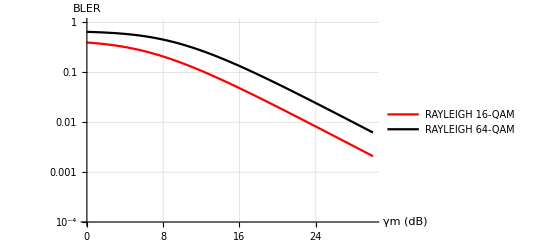

```mathematica
LogPlot[{PeMRAYQAM[γm,16,4], PeMRAYQAM[γm,64,6]},{γm,0,30},AxesLabel->{"γm (dB)","BLER"},PlotRange->{10^-4,1}, PlotStyle->{Red, Black},PlotLegends->{"RAYLEIGH 16-QAM","RAYLEIGH 64-QAM"},GridLines->Automatic]
```

RAYLEIGH PSK:

```mathematica
Q[z_]:=1/2 Erfc[z/(√2)];
pdf[γ_,γm_]:= 1/10^(γm/10)Exp[-γ/10^(γm/10)];
probErrorPSK[γ_]:=Q[√(2 γ)];BERRAYBPSK[γm_] := Re[Integrate[probErrorPSK[γ]×pdf[γ, γm], {γ,0,∞}]];PNmRAYPSK[γm_,N_,m_]:=((N!)/(m!(N-m)!))×(1-BERRAYBPSK[γm])^(N-m)×(BERRAYBPSK[γm])^m;PeMRAYPSK[γm_,N_]:= 1 - PNmRAYPSK[γm,N,0];
```

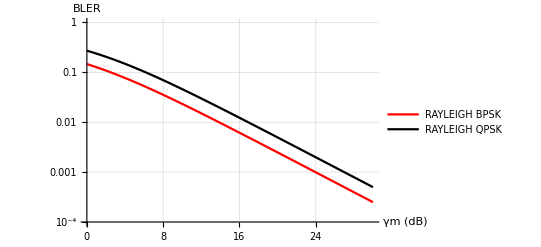

```mathematica
LogPlot[{PeMRAYPSK[γm,1], PeMRAYPSK[γm,2]},{γm,0,30},AxesLabel->{"γm (dB)","BLER"},PlotRange->{10^-4,1}, PlotStyle->{Red, Black},PlotLegends->{"RAYLEIGH BPSK","RAYLEIGH QPSK"},GridLines->Automatic]
```

BLER RAYLEIGH OVER DIFFERENT MODULATIONS:

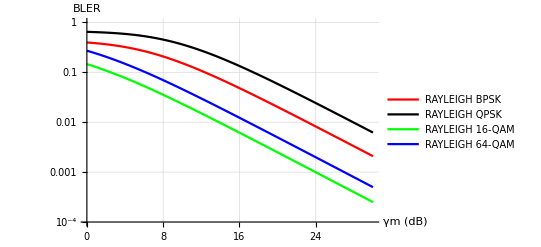

```mathematica
LogPlot[{PeMRAYQAM[γm,16,4], PeMRAYQAM[γm,64,6],PeMRAYPSK[γm,1], PeMRAYPSK[γm,2]},{γm,0,30},AxesLabel->{"γm (dB)","BLER"},PlotRange->{10^-4,1}, PlotStyle->{Red, Black, Green, Blue},PlotLegends->{"RAYLEIGH BPSK","RAYLEIGH QPSK", "RAYLEIGH 16-QAM", "RAYLEIGH 64-QAM"},GridLines->Automatic]
```